1

1

2

2

1

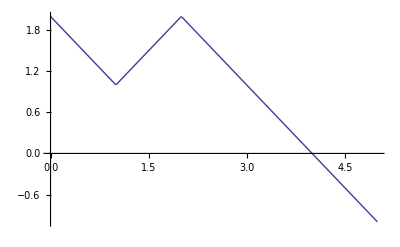

```mathematica
P1=1
v1=1
P2=2
v2=2
a=1
Plot[Piecewise[{{P1+a*(v1-x),0<x≤v1},{x*(P2-P1)/(v2-v1)+(v2*P1-v1*P2)/(v2-v1),v1<x≤v2},{P2+a*(v2-x),v2<x},{0,x<0}}],{x,0,5}]
```